```mathematica
(* notebook to manipulate the stringbit numerical results. *)
(* depends on perturb.nb *)

ClearAll[ResultFolder,LoadEnergyData,LoadTotalEnergy,LoadEvsS];
ResultFolder = NotebookDirectory[]<>"../results/";

LoadTotalEnergy[s_,xi_]:=Module[{file,data},
file = "Es="<> ToString[s] <> "xi="<>ToString[xi];
data = Import[ResultFolder<> file <> ".txt", "Table"];
data=data[[2;;Length[data]]];
Return[data];
];

(*DataSet: 0 for all data point, 1 for odd only, 2 for even only *)
Options[LoadEvsS]={LogData->False,DataSet->0};
LoadEvsS[M_,xi_,opts:OptionsPattern[]]:=Module[{file,data,i,len,ret={}},
file = "Exi="<> ToString[xi] <> "M="<>ToString[M];
data = Import[ResultFolder<> file <> ".txt", "Table"];
data=data[[2;;Length[data]]];
If[OptionValue[LogData],
For[i=1,i≤ Length[data],i++,
data[[i,2]]=Log10[Abs[data[[i,2]]]];
];
];

If[OptionValue[DataSet]==0, Return[data]];

len = Length[data];
For[i=1,i≤Length[data],i++,
If[Mod[data[[i,1]],2]== Mod[OptionValue[DataSet],2],
AppendTo[ret, data[[i]]];
];
];
Return[ret];

(*If[OptionValue[DataSet] == 2,
Return[Table[data[[2*i]],{i,1,Floor[len/2]}]]
];*)
];


(*DataSet: 0 for all data point, 1 for odd only, 2 for even only, 3 for data[L] + data[M-L] *)
Options[LoadEnergyData]={DataSet->0,NormalizeFactorM->0};
LoadEnergyData[s_,xi_,M_,opts:OptionsPattern[]]:=Module[{file,data,dataType, ret, len,normpower},
file = "s="<>ToString[s]<>"-M="<>ToString[M];
If[xi≠0, file = file <> "-xi="<>ToString[xi]];
data=Import[ResultFolder<>file<>".txt","Table"];

normpower = OptionValue[NormalizeFactorM];
data=data[[2;;Length[data],{2,3}]];
Do[data[[i,1]]=N[data[[i,1]]/M];data[[i,2]]=N[data[[i,2]]/(M^normpower)], {i,1,Length[data]}];

dataType = OptionValue[DataSet];
If[dataType == 0,  Return[data]];
len = Length[data];

If[dataType == 3,
Return[Table[{data[[2i-1,1]], data[[2i-1,2]]+data[[len-2i+2,2]]},{i,1,Round[len/2]}]]
];

If[dataType == 1, 
Return[Table[data[[2*i-1]],{i,1,Floor[(len+1)/2]}]]
];

If[dataType == 2,
Return[Table[data[[2*i]],{i,1,Floor[len/2]}]]
];
];

ClearAll[PlotEnergyCorrection];
PlotEnergyCorrection[s_,xi_,Mlist_,showLegends_,opts:OptionsPattern[]]:=Module[{data={},labels={},i,toPlot,m,title,options},
For[i=1,i≤ Length[Mlist],i++,
m = Mlist[[i]];
toPlot=LoadEnergyData[s,xi,m, FilterRules[{opts},Options[LoadEnergyData]]];
AppendTo[data,toPlot];
AppendTo[labels, "M="<>ToString[m]];
];

title = "Change of E with respect to L/M for s="<>ToString[s]<>", ξ="<>ToString[xi];

If[showLegends,
options=Join[{PlotLegends->labels,(*PlotLabel->title,*)AxesLabel->{"i=L/M", "ΔE_i/M^2"}},FilterRules[{opts},Options[ListPlot]]],
options = Join[{AxesLabel->{"i=L/M", "ΔE_i/M^2"}},FilterRules[{opts},Options[ListPlot]]]
];

Return[ListPlot[data,options]]
];

PlotTotalEnergy[sList_,xi_,opts:OptionsPattern[]]:=Module[{data={},labels={},i,j,s},
For[j=1,j≤ Length[sList],j++,
s=sList[[j]];
For[i=1,i≤Length[xi],i++,
AppendTo[data,LoadTotalEnergy[s,xi[[i]]]];
AppendTo[labels, "ξ="<>ToString[xi[[i]]]];
];
];

Return[ListPlot[data,Join[{PlotLegends->labels,AxesLabel->{"M", "ΔE"}},FilterRules[{opts},Options[ListPlot]]]]]
];

PlotEvsS[MList_, xi_, opts:OptionsPattern[]]:=Module[{i,data={},labels={}},
For[i=1,i≤Length[MList],i++,
(*AppendTo[data,LoadEvsS[MList[[i]],xi,LogData->True, DataSet->1]];
AppendTo[data,LoadEvsS[MList[[i]],xi,LogData->True, DataSet->2]];*)
AppendTo[data,LoadEvsS[MList[[i]],xi,FilterRules[{opts},Options[LoadEvsS]]]];
(*AppendTo[labels, "M="<>ToString[MList[[i]]]<>" odd s"];
AppendTo[labels, "M="<>ToString[MList[[i]]] <> " even s"];*)
AppendTo[labels, "M="<>ToString[MList[[i]]]];
];

Return[ListPlot[data,Join[{PlotLegends->labels,AxesLabel->{"s", "Log|ΔE|"},PlotMarkers->Automatic},FilterRules[{opts},Options[ListPlot]]]]]
];

DltEArray={{3,-0.294229},{5,1.51612},{7,8.84788},{9,24.8366},{11,52.4987},{13,94.7675},{15,154.512},{17,234.55},{19,337.654},{21,466.562},{23,623.977},{25,812.573},{27,1035},{29,1293.88}};
DeltaE[M_,x_]:=-4Cot[Pi/(2*M)]+DltEArray[[(M-1)/2,2]]*x^2;

ClearAll[PlotLowestEnergy];
PlotLowestEnergy[M_,minN_,maxN_,color_]:=Module[{file,mat1,mat2,mat3,mat4,cmat,vmat, plot},
file = ToString[M]<>"h0Ham-";
mat1=LoadSparseMatFromFile[file <> "re-0.dat"];
mat2=LoadSparseMatFromFile[file <> "re-1.dat"];
mat3=LoadSparseMatFromFile[file <> "im-0.dat"];
mat4=LoadSparseMatFromFile[file <> "im-1.dat"];
cmat=N[mat1 + I*mat3];
vmat = N[mat2 + I * mat4];

plot=Plot[{-Re[First[Eigenvalues[-cmat - vmat *x,1,Method->{Arnoldi,MaxIterations->10^5,Criteria->RealPart}]]],DeltaE[M,x]},
{x,N[1/maxN],N[1/minN]+.2},PlotStyle->{Directive[color,Dashed],color},AxesOrigin->Automatic,AxesLabel->{"1/N","E"}, PlotLegends->LineLegend[{color},{"M="<>ToString[M]}]
];

Return[plot];
];
```

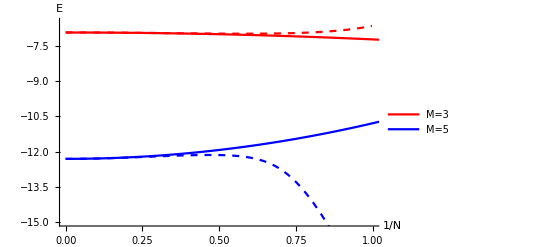

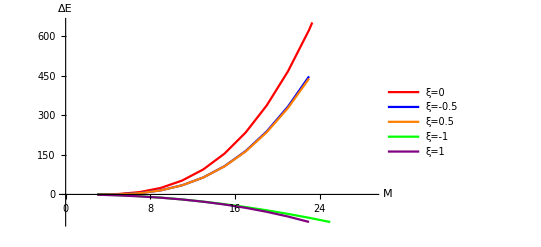

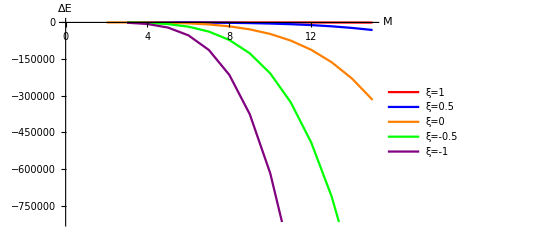

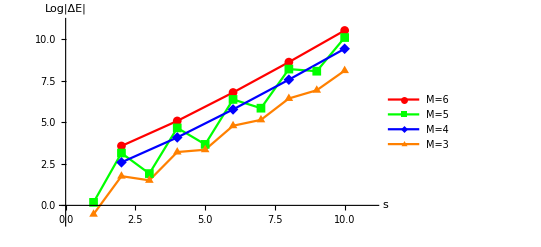

```mathematica
(* compare the 1/N^2 correction to the exact energy. *)
p1=PlotLowestEnergy[3,1,Infinity,Red];
p2=PlotLowestEnergy[5,1,Infinity,Blue];
Show[p1,p2,PlotRange->{{0,1}, {-15,-6.5}},AxesOrigin->Automatic]
Export["EvM-compare.pdf",%];

(* This cell investigates how E changes with respect to ξ *)
PlotTotalEnergy[{1},{0,-0.5,0.5,-1,1},Joined->True,PlotStyle->{Red,Blue,Orange,Green,Purple}]
Export["EvM-s1-manyxi.pdf",%];
PlotTotalEnergy[{2},{1,0.5,0,-0.5,-1},Joined->True,PlotStyle->{Red,Blue,Orange,Green,Purple}]
Export["EvM-s2-manyxi.pdf",%];
(* investigate how Delta E change with respect to s*)
PlotEvsS[{6,5,4,3},0,Joined->True,LogData->True, DataSet->0,PlotStyle->{Red, Green, Blue, Orange},PlotRange->{{0,11},{-1,11}}, AxesOrigin->{0,0}]
Export["EvS-xi0.pdf",%];
```

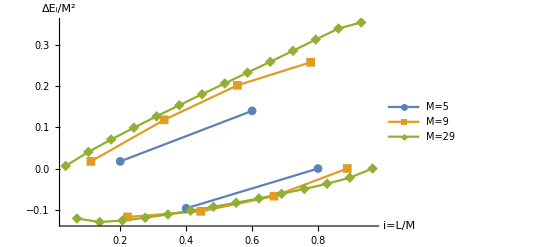

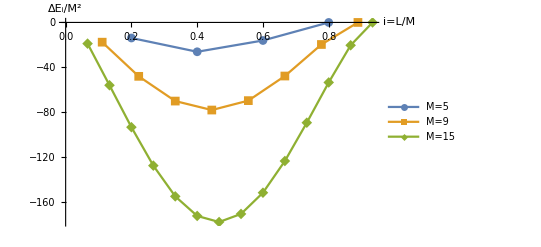

```mathematica
(* This cell demostrate how Delta Subscript[E, i] changes with respect to i=L/M.*)
p1=PlotEnergyCorrection[1,0,{5,9,29},True, DataSet->1,NormalizeFactorM->2,Joined->True,PlotMarkers->Automatic];
(*Export["SubEvM-s1xi0-a.pdf",%];*)
p2=PlotEnergyCorrection[1,0,{5,9,29}, False,DataSet->2,NormalizeFactorM->2,Joined->True,PlotMarkers->Automatic];
Show[p1,p2, PlotRange->Automatic]
Export["SubEvM-s1xi0.pdf",%];
PlotEnergyCorrection[2,0,{5,9,15}, True,DataSet->0,NormalizeFactorM->2,Joined->True,PlotMarkers->Automatic]
Export["SubEvM-s2xi0.pdf",%];
(*p1=PlotEnergyCorrection[1,0,{5,9,15,19,29}, DataSet->3,NormalizeFactorM->2,Joined->True];
p2=Plot[x/4,{x,0,1}, PlotStyle->Dashed, PlotLegends->{"L/(4M)"}];
Show[p1,p2]
(*Export["SubEvM-s1xi0-c.pdf",%];*)*)
```